## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/stricklandlab/Desktop/quenching_cuba_integration/mathematica

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

## Load params

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
myDict=Association[Table[myParams[[i,1]]->ToExpression[myParams[[i,2]]],{i,1,Length[myParams]}]];
```

{{nc,3},{alphas,0.5},{massQQ,9.46},{lambdaQCD,0.25},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1},{}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

ToExpression::notstrbox: {{nc,3},{alphas,0.5},{massQQ,9.46},{lambdaQCD,0.25},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1},{}}⟦12,2⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ToExpression::notstrbox: {{nc,3},{alphas,0.5},{massQQ,9.46},{lambdaQCD,0.25},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1},{}}⟦18,2⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

```mathematica
(* load variables from params file to automate some things below *)
M = myDict["massQQ"]
roots = myDict["rootsnn"]
```

9.46

5023

## General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

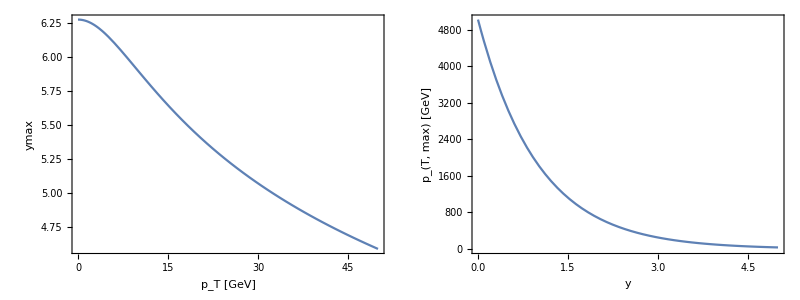

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

## Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output/pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5}]
```

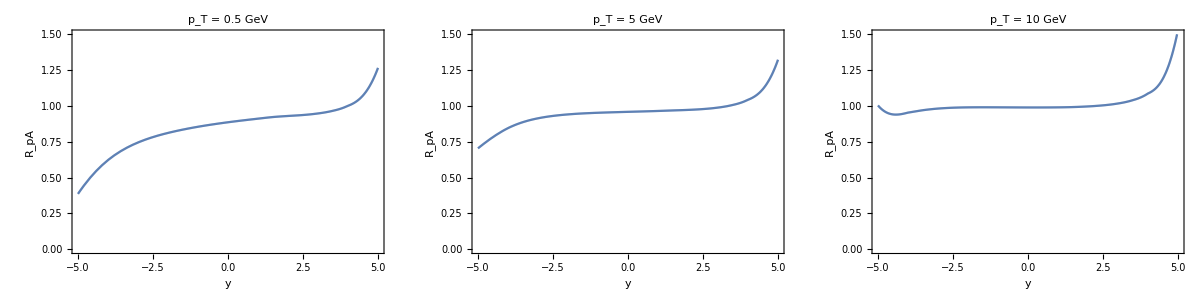

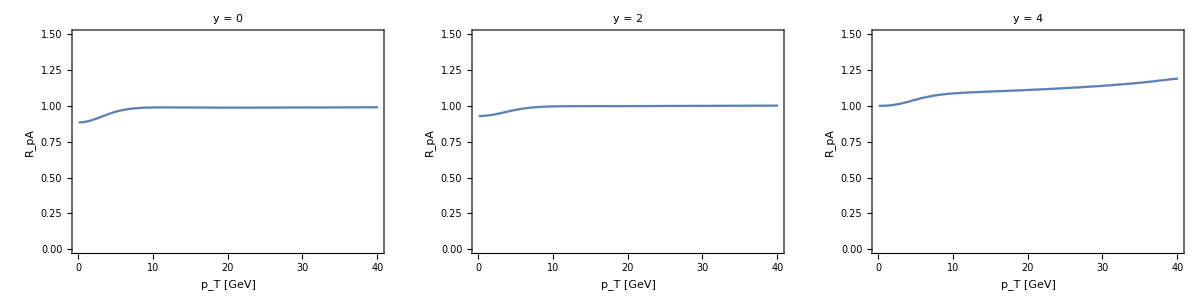

```mathematica
Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
Grid[{{mypAPlotPT[0],mypAPlotPT[2],mypAPlotPT[4]}}]
```